# Lesson 1 log · Sequence to sequence with deep LSTMs

Written 2026-11-24 01:47 UTC by lesson1_lstm_seq2seq.nb. 19 of 19 checks pass.

Paper: I. Sutskever, O. Vinyals, Q. V. Le, Sequence to Sequence Learning with Neural Networks, NeurIPS 2014, arXiv:1409.3215. Each part is coded from plain arrays in lesson1_lstm_seq2seq.nb and checked against Wolfram's layers. The trained demo nets for this paper are in ref1_seq2seq_sutskever2014.nb.

## 1. The LSTM cell

An LSTM keeps a hidden state h and a memory cell c. Each step reads one input vector x and computes four gates; the memory is updated by addition, which is what lets information and gradients survive across long sentences.

i = σ(Wi·x + Ui·h + bi)    f = σ(Wf·x + Uf·h + bf)    o = σ(Wo·x + Uo·h + bo)
g = tanh(Wg·x + Ug·h + bg)
c' = f×c + i×g        h' = o×tanh(c')

PASS  the cell coded from arrays gives the same hidden states as LongShortTermMemoryLayer (7 steps, 4 inputs, 6 cells)

PASS  it also agrees when it starts from given states h0, c0 (the decoder's situation)

In Wolfram the four gates are the arrays InputGate…, ForgetGate…, OutputGate… and MemoryGate… of LongShortTermMemoryLayer; the ports State and CellState are h and c, and are reached through NetGraph (sqWithStates).

## 2. The deep LSTM encoder and the thought vector

The paper stacks four LSTMs: layer k reads the hidden states of layer k−1. After the last source word, the final (h, c) of every layer together form a fixed-size summary of the whole sentence. The decoder starts from it.

PASS  a 3-layer stack coded from arrays matches NetChain of three LongShortTermMemoryLayers

PASS  the thought vector of the paper's model has 2 × 4 × 1000 = 8000 numbers (paper, Section 3.4)

## 3. The decoder step

The decoder is a second deep LSTM with its own weights (the paper uses two different LSTMs). It starts from the encoder's final states, reads the embedding of the previous output word, and a softmax over the target vocabulary gives the probability of the next word.

p(y_t | y_<t, x) = softmax(W·h_t + b),   h_t from the top decoder layer

PASS  the decoder's next-word distribution is a probability distribution over the 10 target words

PASS  the decoder's first layer, started from the encoder's states, matches LongShortTermMemoryLayer with State and CellState given

## 4. Reversing the source sentence

Instead of mapping a, b, c to α, β, γ, the LSTM maps c, b, a to α, β, γ. Put the source words at positions 1…T and the target words at T+1…2T, with target word i aligned to source word i. The table gives the distance between each aligned pair for T = 8.

pair i | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
forward | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
reversed | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15

PASS  reversal leaves the average distance unchanged (8)

PASS  but cuts the shortest distance from T = 8 to 1, so the first words can 'communicate' at once

The paper reports test perplexity falling from 5.8 to 4.7 and BLEU rising from 25.9 to 30.6 with reversed sources (Section 3.3).

## 5. Uniform initialisation in [−0.08, 0.08]

All parameters start uniformly distributed in [−0.08, 0.08] (Section 3.4). In Wolfram, NetInitialize does this with one option, except for the LSTM forget-gate biases, which it always sets to 1 (a later practice: Jozefowicz, Zaremba and Sutskever, 2015). sqUniformInit resets those too.

NetInitialize[net, All, Method -> {"Random", "Weights" -> UniformDistribution[{-0.08, 0.08}], "Biases" -> UniformDistribution[{-0.08, 0.08}]}]
then NetReplacePart[net, {k, "ForgetGateBiases"} -> RandomVariate[UniformDistribution[{-0.08, 0.08}], n]]

PASS  NetInitialize alone sets the forget-gate biases to 1, so the paper's rule needs one more step

PASS  after sqUniformInit, every one of the 5760 parameters of a 2-layer LSTM lies in [−0.08, 0.08]

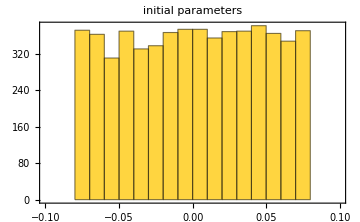

## 6. Clipping the gradient by its norm

LSTMs rarely have vanishing gradients but can have exploding ones. For each batch the paper computes the norm s of the whole gradient g (all parameters together) and, if s > 5, rescales g to 5 g / s (Section 3.4).

s = ‖g‖₂ ;   if s > 5 :  g ← 5 g / s

PASS  after clipping, the norm is 5 (it was 13.8)

PASS  the direction is unchanged: cosine(g, clipped g) = 1

PASS  clamping each component to [−1, 1] instead turns the direction (cosine 0.915)

PASS  a small gradient is left alone

## 7. The learning-rate schedule

Plain stochastic gradient descent without momentum, learning rate 0.7. After 5 epochs the rate is halved every half epoch; training stops after 7.5 epochs. Batches hold 128 sentences (Section 3.4).

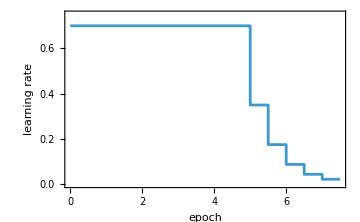

PASS  0.7 up to epoch 5, then 0.35, 0.175, … down to 0.7/32 in the last half epoch

## 8. Beam search

The decoder is run left to right, keeping the B most likely partial translations. Each is extended by every word; the B best of all the extensions are kept. A hypothesis that ends in <EOS> leaves the beam and joins the finished list. The paper finds that even B = 1 works well and that B = 2 gives most of the benefit (Section 3.2).

Toy model: the first word is A (0.6) or B (0.4). After A the model hesitates (A, B: 0.35; <e>: 0.3); after B it almost always stops (<e>: 0.95). Greedy decoding takes A and is trapped; a beam of width 2 keeps B alive.

width | best output | probability
1 |   AAAAAA | 0.00315
2 |   B<e> | 0.38

PASS  the beam of width 2 finds 'B <e>' with probability 0.38

PASS  greedy decoding (width 1) ends with a less likely output

## 9. The parameter count of the paper's model

An LSTM layer with nIn inputs and n cells has four gates, each with n×nIn input weights, n×n state weights and n biases: 4(n·nIn + n.b2 + n).

source embeddings 160,000 × 1000 | 160,000,000
target embeddings 80,000 × 1000 | 80,000,000
encoder: 4 LSTM layers of 1000 cells | 32,016,000
decoder: 4 LSTM layers of 1000 cells | 32,016,000
softmax 80,000 × 1000 + 80,000 | 80,080,000
total | 384,112,000

PASS  the formula agrees with Wolfram's count for an LSTM layer with 4 inputs and 6 cells (264)

PASS  the total is 384,112,000: the paper's '384M parameters' (Section 3.4)

## Where this is used in TensorNets

tnParserNet is a transformer rather than an LSTM (Lesson 3), but three ideas come from this paper: an encoder–decoder that reads the whole input before writing, beam search over the decoder, and clipping the gradient by its norm.

© Computational Classnotes · CC BY-NC-SA 4.0